```mathematica
Clear["Global`*"];
```

```mathematica
λ=λ/.FindRoot[E^λ==λ^2/(0.244 6.1 10^-10 π^2),{λ,25}]
```

26.9248

```mathematica
M=1.22 10^22;
G=1/M^2;
Subscript[G, F]=1/((3*10^5)^2);
s=10^22/6.58;
g[n_]:=2+7/8 2n(11/4)^(4/3);
```

```mathematica
Δm=1.2933;
Tn[n_:3]:=((1.66 √g[n])/(30 1.2 M Subscript[G, F]^2))^(1/3);
Td=(*0.065;*)2.22/λ
```

0.0824519

```mathematica
Tn[3]
Tn[3+7/8 4]
Tn[19]
```

0.524555

0.591782

0.704195

```mathematica
t[T_,g_]:=M/(2 T^2 1.66 √g);
Δ[nd_,nn_]:=(t[Td,g[nd]]-t[Tn[nn],g[nn]])/s;
τ=885.7;
np[nd_,nn_]:=N[E^(-Δm/Tn[nn])E^(-Δ[nd,nn]/τ)]
```

```mathematica
Δ[3,19]
np[3,19]
```

75.1129

0.146406

```mathematica
He[nd_,nn_]:=(2np[nd,nn])/(1+np[nd,nn])
```

```mathematica
He[3,19]
He[3.046,19]
He[4,20]
```

0.255417

0.255549

0.261258

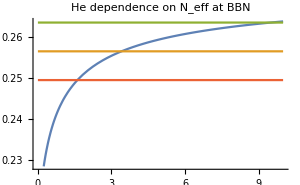
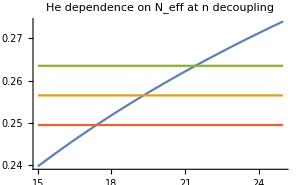

-Graphics3D-

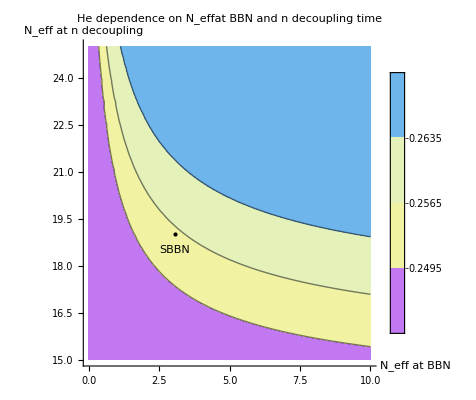

```mathematica
Row[{
Plot[{He[n,19],0.2565,0.2635,0.2495},{n,0,10},PlotLabel->"He dependence on N_eff at BBN",ImageSize->300],
Plot[{He[3,n],0.2565,0.2635,0.2495},{n,15,25},PlotLabel->"He dependence on N_eff at n decoupling",ImageSize->300]
}]
Plot3D[{He[n,m],0.2565,0.2635,0.2495},{n,0,10},{m,15,25},PlotStyle->{,Opacity[0.3],Opacity[0.3],Opacity[0.3]},PlotRange->All]
ContourPlot[He[nd,nn],{nd,0,10},{nn,15,25},Contours->{0.2495,0.2565,0.2635},PlotLegends->Automatic,ColorFunction->ColorData["Pastel"],AxesLabel->{"N_eff at BBN","N_eff at n decoupling"},Frame->False,Axes->True,Epilog->{PointSize[Large],Point[{3.046,19}],Text["SBBN",{3.046, 18.5}]},PlotLabel->"He dependence on N_effat BBN and n decoupling time"]
```